# ProjectBlaze

```mathematica
Share[]
```

1774120

```mathematica
SetDirectory[
"C:\\Users\\hilma\\OneDrive\\Documents\\Post Project\\MSTM\\MSTM-main\\post"]
```

C:\Users\hilma\OneDrive\Documents\Post Project\MSTM\MSTM-main\post

```mathematica
nfread[file_]:=Module[{f,dat,sdat,pos,n,c,cdim,tdat,gmin,gmax,nb,bdat},f=OpenRead[file];
tdat={};
Do[
pos=Find[f," run number"];
If[ToString[pos]=="EndOfFile",Break[]];
n=Read[f,Number];
n=Read[f,Number];
If[n>0,c=ReadList[f,Table[Number,{4}],n],c={}];
sdat={n,c};
n=Read[f,Number];
If[n>0,c=ReadList[f,Number,n],c={}];
bdat={n,c};
gmin=Read[f,Table[Number,{3}]];
gmax=Read[f,Table[Number,{3}]];
cdim=Read[f,Table[Number,{3}]];
n=cdim[[1]]cdim[[2]]cdim[[3]];
dat=ReadList[f,Table[Number,{27}],n];
tdat=Append[tdat,{cdim,{gmin,gmax},sdat,bdat,dat}];
,{i,1,1000}];
Close[f];
tdat]
cplot[tdat_]:=Module[{cdim,rmin,rmax,splot,nb,bplot,ep,b,arat},
cdim=tdat[[1]];
p=Which[cdim[[1]]==1,1,cdim[[2]]==1,2,cdim[[3]]==1,3];
rmin=Drop[tdat[[2,1]],{p}];rmax=Drop[tdat[[2,2]],{p}];
ppos=tdat[[2,1,p]];
ns=tdat[[3,1]];sdat=tdat[[3,2]];
nis=0;ispos={};israd={};
Do[
t1=Abs[sdat[[i,p]]-ppos];
If[t1<sdat[[i,4]],
nis=nis+1;
ispos=Append[ispos,Drop[sdat[[i,{1,2,3}]],{p}]];
israd=Append[israd,Sqrt[sdat[[i,4]]^2-t1^2]];
];
,
{i,1,ns}];
splot=Table[Circle[ispos[[i]],israd[[i]]],{i,1,nis}];
nb=tdat[[4 ,1]];b=tdat[[4,2]];
bplot=If[nb>0,Table[Line[{{rmin[[1]],b[[i]]},{rmax[[1]],b[[i]]}}],{i,1,nb}],{}];
ep=Epilog->{splot,bplot};
arat=AspectRatio->Which[p==1,cdim[[3]]/cdim[[2]],p==2,cdim[[3]]/cdim[[1]],p==3,cdim[[2]]/cdim[[1]]];
{ep,arat}]
readmstm[file_,vars_,len_]:=Module[{f,newlist,str,dat,pos,tdat,t1},
f=OpenRead[file];
newlist=" input variables";
str=Find[f,newlist];
dat={};
Do[
pos=StreamPosition[f];
tdat=Table[Null[],{Length[vars]}];
Do[
str=ToString[Find[f,{newlist,vars[[j]]}]];
If[str==ToString[EndOfFile],Break[]];
If[Length[StringCases[str,vars[[j]]]]!=0,
t1=Read[f,Table[Number,{len[[j]]}]][[len[[j]]]];
tdat[[j]]=t1;
];
SetStreamPosition[f,pos];
,{j,1,Length[vars]}];
dat=Append[dat,tdat];
str=ToString[Find[f,newlist]];
If[str==ToString[EndOfFile],Break[]];
,{i,1,100000}];
Close[f];
dat]
```

## BlazeTest

```mathematica
vars={" length, ref index"," total extinction, absorption"," total extinction, absorption"," total extinction, absorption"};
len={1,3,2,1};
dat=readmstm["blazetest.dat",vars,len];
wav=2 Pi / dat[[All,1]];
```

```mathematica
g=Table[ListPlot[{Table[{wav[[j]],dat[[j,i]]},{j,1,Length[wav]}]},Frame->True,Axes->False,FrameStyle->Medium,Joined->True,AspectRatio->1,FrameLabel->{"wavelength",""},PlotRangePadding->None],{i,2,Length[vars]}];
```

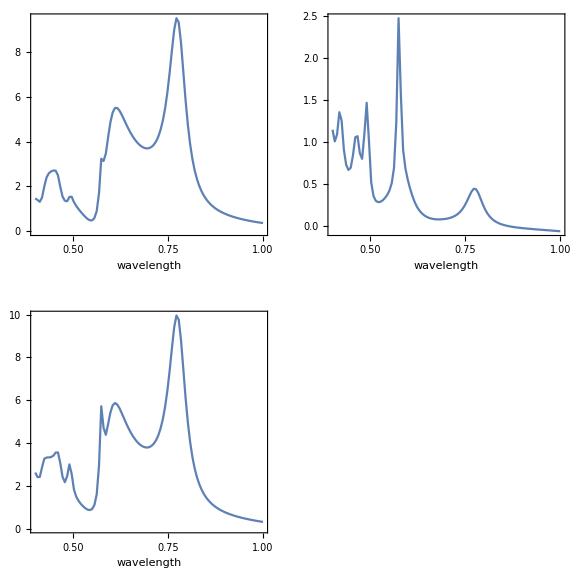

```mathematica
g2=GraphicsGrid[{{g[[1]],g[[2]]},{g[[3]]}},ImageSize->Large]
```

## Heterogeneous Dispersive Spheres

```mathematica
vars={"   sphere    host"," total extinction, absorption"," total extinction, absorption"," total extinction, absorption"};
len={4,3,2,1};
dat=readmstm["het_dispersive.dat",vars,len];
wav=(2 Pi)/dat[[All,1]] 0.1;
```

```mathematica
g=Table[ListPlot[{Table[{wav[[j]],dat[[j,i]]},{j,1,Length[wav]}]},Frame->True,Axes->False,FrameStyle->Medium,Joined->True,AspectRatio->1,FrameLabel->{"wavelength",""},PlotRangePadding->None],{i,2,Length[vars]}];
```

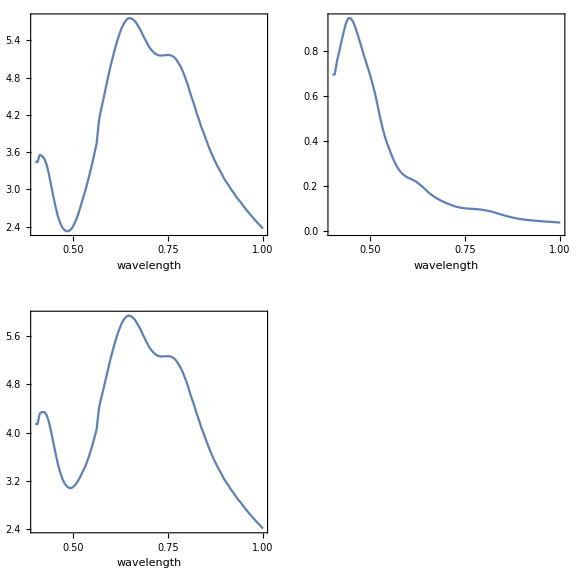

```mathematica
g2=GraphicsGrid[{{g[[1]],g[[2]]},{g[[3]]}},ImageSize->Large]
```

## Blaze1

```mathematica
ndat=nfread["blaze1a-nf.dat"];
{ep,arat}=cplot[ndat[[1]]];
pdat=ndat[[1,-1]];
```

```mathematica
pl={12,18,22,26};
```

```mathematica
g=Table[ListContourPlot[pdat[[All,{1,3,pl[[i]]}]],PlotRange->All,PlotRangePadding->None,ep,arat,Contours->20,ColorFunction->"Rainbow"],{i,1,Length[pl]}];
```

```mathematica
g2=GraphicsGrid[{{g[[1]],g[[2]]},{g[[3]],g[[4]]}},ImageSize->Large]
```

-Graphics-

Clockwise from top left: H_(y,1),E_(y,2), H_(z,2), H_(x,2), with second subscript 1,2 denoting incident polarization parallel or perpendicular to plane.

```mathematica
vars={" length, ref index"," total extinction, absorption"," total extinction, absorption"," total extinction, absorption"};
len={1,3,2,1};
dat=readmstm["blaze1b.dat",vars,len];
wav=2 Pi / dat[[All,1]];
```

```mathematica
g=Table[ListPlot[{Table[{wav[[j]],dat[[j,i]]},{j,1,Length[wav]}]},Frame->True,Axes->False,FrameStyle->Medium,Joined->True,AspectRatio->1,FrameLabel->{"wavelength",""},PlotRangePadding->None],{i,2,Length[vars]}];
```

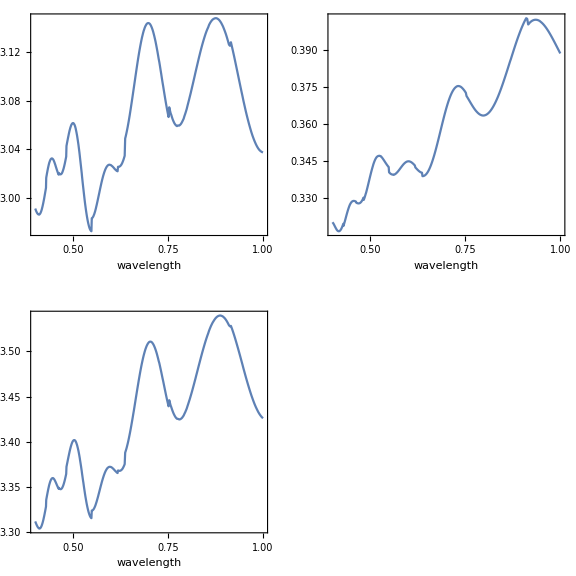

```mathematica
g2=GraphicsGrid[{{g[[1]],g[[2]]},{g[[3]]}},ImageSize->Large]
```

top left to right: scattering cross section, absorption cross section
bottom: extinction cross section

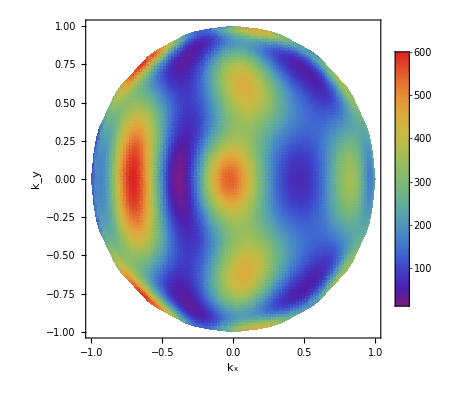

```mathematica
filesmk=OpenRead["blaze1a.dat"];
dot=7845;
Find[filesmk,"    kx      ky"];
datsmb=ReadList[filesmk, Table[Number, {18}],dot];
Find[filesmk,"    kx      ky"];
datsmf=ReadList[filesmk, Table[Number, {18}],dot];
smsm={};
Do[
smsm=Append[smsm, datsmb[[i,{1,2,3}]]];,
{i,Length[datsmb]}];
Do[
smsm=Append[smsm, datsmf[[i,{1,2,3}]]];,
{i,Length[datsmf]}];
g=ListDensityPlot[smsm,PlotRangePadding->None,FrameLabel->{"k_x","k_y"},ColorFunction->"Rainbow",PlotLegends->Automatic]
```

phase function plot with k_x=Sin[θ]Cos[ϕ], k_y=Sin[θ]Sin[ϕ]

## Blaze2

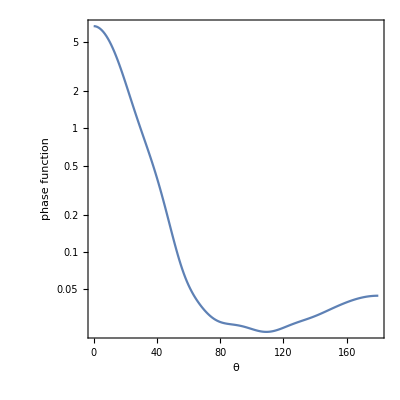

```mathematica
filesmt=OpenRead["blaze2a.dat"];
Find[filesmt,"number directions, number"];
tn=Read[filesmt,Table[Number,{2}]];
Find[filesmt,"  theta     11"];
datsm=ReadList[filesmt, Table[Number, {tn[[2]]+1}],tn[[1]]];
smsm=Table[datsm[[i,{1,2}]],{i,Length[datsm]}];
g=ListLogPlot[smsm,Frame->True,Axes->True,FrameStyle->Medium,Joined->True,AspectRatio->1,FrameLabel->{"θ","phase function"},PlotRangePadding->None]
```

```mathematica
vars={" length, ref index"," total extinction, absorption"," total extinction, absorption"," total extinction, absorption"};
len={1,3,2,1};
dat=readmstm["blaze2b.dat",vars,len];
wav=2 Pi 0.1 / dat[[All,1]];
```

```mathematica
g=Table[ListPlot[{Table[{wav[[j]],dat[[j,i]]},{j,1,Length[wav]}]},Frame->True,Axes->False,FrameStyle->Medium,Joined->True,AspectRatio->1,FrameLabel->{"wavelength",""},PlotRangePadding->None],{i,2,Length[vars]}];
```

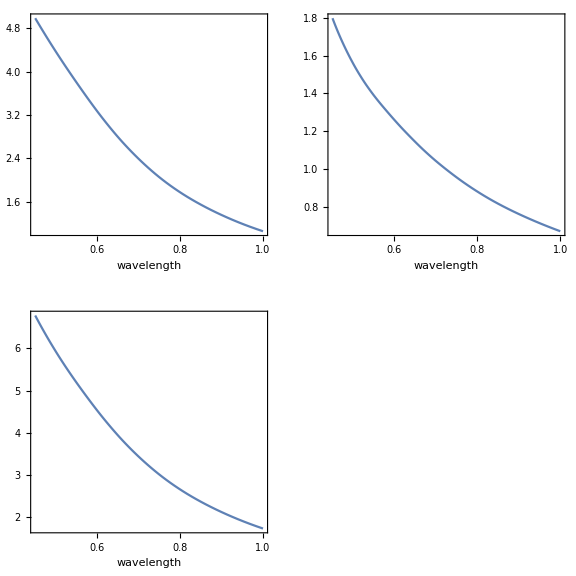

```mathematica
g2=GraphicsGrid[{{g[[1]],g[[2]]},{g[[3]]}},ImageSize->Large]
```